0.394516

0.000137337

-0.434107

0.000872172

0.420883

-0.00181892

-0.397624

-0.000351558

0.364948

-0.000412

-0.326192

0.000994309

0.283822

1.

0.111291+0.0000671032 Cos[θ]-0.136914 (-1+3 Cos[θ]^2)+0.000325474 (-3 Cos[θ]+5 Cos[θ]^3)+0.0445233 (3-30 Cos[θ]^2+35 Cos[θ]^4)-0.000212723 (15 Cos[θ]-70 Cos[θ]^3+63 Cos[θ]^5)-0.0252766 (-5+105 Cos[θ]^2-315 Cos[θ]^4+231 Cos[θ]^6)-0.0000240059 (-35 Cos[θ]+315 Cos[θ]^3-693 Cos[θ]^5+429 Cos[θ]^7)+0.0033162 (35-1260 Cos[θ]^2+6930 Cos[θ]^4-12012 Cos[θ]^6+6435 Cos[θ]^8)-3.95785×10^-6 (315 Cos[θ]-4620 Cos[θ]^3+18018 Cos[θ]^5-25740 Cos[θ]^7+12155 Cos[θ]^9)-0.00164717 (-63+3465 Cos[θ]^2-30030 Cos[θ]^4+90090 Cos[θ]^6-109395 Cos[θ]^8+46189 Cos[θ]^10)+5.25461×10^-6 (-693 Cos[θ]+15015 Cos[θ]^3-90090 Cos[θ]^5+218790 Cos[θ]^7-230945 Cos[θ]^9+88179 Cos[θ]^11)+0.000390941 (231-18018 Cos[θ]^2+225225 Cos[θ]^4-1021020 Cos[θ]^6+2078505 Cos[θ]^8-1939938 Cos[θ]^10+676039 Cos[θ]^12)

-Graphics3D-

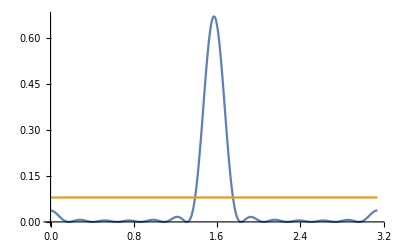

```mathematica
m1Y00=0.394516
m1Y01=0.000137337
m1Y02=-0.434107
m1Y03=0.000872172
m1Y04=0.420883
m1Y05=-0.00181892
m1Y06=-0.397624
m1Y07=-0.000351558
m1Y08=0.364948
m1Y09=-0.000412
m1Y010=-0.326192
m1Y011=0.000994309
m1Y012=0.283822
NConst =1.00
m1[θ_]=m1Y00*SphericalHarmonicY[0,0,θ,0]+m1Y01*SphericalHarmonicY[1,0,θ,0]+m1Y02*SphericalHarmonicY[2,0,θ,0]+m1Y03*SphericalHarmonicY[3,0,θ,0]+m1Y04*SphericalHarmonicY[4,0,θ,0]+m1Y05*SphericalHarmonicY[5,0,θ,0]+m1Y06*SphericalHarmonicY[6,0,θ,0]+m1Y07*SphericalHarmonicY[7,0,θ,0]+m1Y08*SphericalHarmonicY[8,0,θ,0]+m1Y09*SphericalHarmonicY[9,0,θ,0]+
m1Y010*SphericalHarmonicY[10,0,θ,0]+m1Y011*SphericalHarmonicY[11,0,θ,0]+m1Y012*SphericalHarmonicY[12,0,θ,0]

SphericalPlot3D[{((1/NConst)*m1[θ])^2, 1/(4 π)},{θ,0,π},{ϕ,0,π}, PlotRange -> All]
Plot[{((1/NConst)*m1[θ])^2, 1/(4 π)},{θ,0,π}, PlotRange -> All]
```

```mathematica
Export["D:\\Documents\\College\\OSU\\Research\\Sph. Harmonics proj\\SphHarEvol.1.cpp\\SphHarEvol.1.1\\Corrected 90-15-300 with 10 Species 2D.jpg",%175,"JPEG"]
```

D:\Documents\College\OSU\Research\Sph. Harmonics proj\SphHarEvol.1.cpp\SphHarEvol.1.1\Corrected 90-15-300 with 10 Species 2D.jpg

```mathematica
Export["D:\\Documents\\College\\OSU\\Research\\Sph. Harmonics proj\\SphHarEvol.1.cpp\\SphHarEvol.1.1\\Corrected 90-15-300 with 10 Species.jpg",%155,"JPEG"]
```

D:\Documents\College\OSU\Research\Sph. Harmonics proj\SphHarEvol.1.cpp\SphHarEvol.1.1\Corrected 90-15-300 with 10 Species.jpg

```mathematica
Simplify[NConst]
```

1.

```mathematica
N[Integrate[Sin[θ](m1[θ])^2 , {θ,0,Pi},{ϕ,0,2 Pi}]]
```

0.999488

```mathematica
Integrate[1/(4 π)Sin[θ], {θ,0,Pi},{ϕ,0,2 Pi}]
```

1

```mathematica
Simplify[1/3(3/(4 Pi))^(1/1)]
```

1/(4 π)

```mathematica
Show[%724,ViewPoint->{0,-∞,0}]
```

Information::notfound: Symbol Delta not found.

```mathematica
SphericalPlot3D[{ (1/NConst)*SphericalHarmonicY[0,0,θ,ϕ]+(2/NConst)*SphericalHarmonicY[1,0,θ,ϕ] , (3/(4 Pi))^(1/3) },{θ,0,Pi},{ϕ,0,Pi}, PlotRange -> All]
```

-Graphics3D-

```mathematica
SphericalPlot3D[{ (2/NConst)*SphericalHarmonicY[1,0,θ,ϕ] , (3/(4 Pi))^(1/3) },{θ,0,Pi},{ϕ,0,Pi/2}, PlotRange -> All]
```

-Graphics3D-

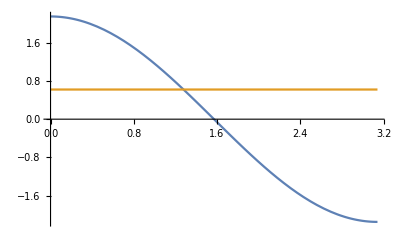

1.

```mathematica
Plot[{(2/NConst)*SphericalHarmonicY[1,0,θ,0] , (3/(4 Pi))^(1/3) },{θ,0,Pi}, PlotRange -> All]
```

```mathematica
N[m1[π/1.001]^2 * Sin[π/1.001]]
```

0.000382591